# Modelo CAM Random Forest

## Database

#### Importing data

```mathematica
dfList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa2.csv"];
dateList = DateObject[{ToExpression[StringTake[#, {7, 10}]], 
                                ToExpression[StringTake[#, {4, 5}]], 
                                ToExpression[StringTake[#, {1, 2}]]}] & /@ 
                                (Rest[dfList[[All,2]]]);
dfAssociation=AssociationThread[dfList[[1]]->#]&/@Rest[dfList];
dfAssociation=MapThread[Append[#1, "DateConverted" -> #2] &, {dfAssociation, dateList}];
dfDataSet=Dataset[dfAssociation];
dfDataSet = dfDataSet[All, Append[#, "Total" -> (#FTHG + #FTAG)] &];
dfDataSet = dfDataSet[All, Append[#, "DifferenceGoals" -> Abs[#FTHG - #FTAG]] &];
```

```mathematica
trainingCutoffDate = DateObject[{2023,01,01},"Day"];
trainDataSet = dfDataSet[Select[#DateConverted <= trainingCutoffDate &]];
testDataSet = dfDataSet[Select[#DateConverted > trainingCutoffDate &]];
```

#### Creating ELO

```mathematica
(* Inicializar parámetros ELO *)
initialElo = 1500;
kFactor = 10;
(* Función para calcular la puntuación esperada *)
expectedScore[ratingA_, ratingB_] := 1/(1 + 10^((ratingB - ratingA)/400));
(* Función para actualizar la calificación ELO *)
updateElo[currentRating_, expected_, actual_] := currentRating + kFactor * (actual - expected);
(* Inicializar diccionario de calificaciones ELO *)
eloRatings = <||>;
(* Procesar cada partido del conjunto de entrenamiento para actualizar las calificaciones ELO *)
trainDataSet[All, 
  Function[match, 
   Module[{homeTeam, awayTeam, homeGoals, awayGoals, homeRating, 
     awayRating, homeExpected, awayExpected, homeActual, awayActual},
    
    homeTeam = match["HomeTeam"];
    awayTeam = match["AwayTeam"];
    homeGoals = match["FTHG"];
    awayGoals = match["FTAG"];
    
    (* Inicializar calificaciones ELO si los equipos no están calificados *)
    If[!KeyExistsQ[eloRatings, homeTeam], 
     eloRatings[homeTeam] = initialElo];
    If[!KeyExistsQ[eloRatings, awayTeam], 
     eloRatings[awayTeam] = initialElo];
    
    (* Obtener calificaciones actuales *)
    homeRating = eloRatings[homeTeam];
    awayRating = eloRatings[awayTeam];
    
    (* Calcular puntuaciones esperadas *)
    homeExpected = expectedScore[homeRating, awayRating];
    awayExpected = expectedScore[awayRating, homeRating];
    
    (* Determinar puntuaciones reales basadas en el resultado del partido *)
    Which[
     homeGoals > awayGoals, homeActual = 1; awayActual = 0;,
     homeGoals < awayGoals, homeActual = 0; awayActual = 1;,
     True, homeActual = 0.5; awayActual = 0.5
    ];
    
    (* Actualizar calificaciones *)
    eloRatings[homeTeam] = updateElo[homeRating, homeExpected, homeActual];
    eloRatings[awayTeam] = updateElo[awayRating, awayExpected, awayActual];
    ]
   ]];
(* Convertir las calificaciones ELO finales a una lista y ordenarlas por calificación *)
finalEloRatings = SortBy[Normal[eloRatings], -Last[#] &];
(* Convertir las calificaciones finales a una asociación *)
finalEloRatingsAssociation = Association[finalEloRatings];
(* Crear una función para obtener el ELO rating de un equipo *)
getEloRating[team_, eloAssoc_] := team /. eloAssoc;
(* Aplicarlo a equipo local *)
homeTeamELOList = getEloRating[#, finalEloRatingsAssociation]&/@ trainDataSet[All, "HomeTeam"]//Normal;
trainDataSet = Dataset[MapThread[Append[#1, "HomeTeamELO" -> #2] &, {trainDataSet//Normal, homeTeamELOList}]];
(* Aplicarlo a equipo visitante *)
awayTeamELOList = getEloRating[#, finalEloRatingsAssociation]&/@ trainDataSet[All, "AwayTeam"]//Normal;
trainDataSet = Dataset[MapThread[Append[#1, "AwayTeamELO" -> #2] &, {trainDataSet//Normal, awayTeamELOList}]];
(* Obtener diferencias de ELO *)
trainDataSet = trainDataSet[All,Append[#,"DifferenceELO"->#HomeTeamELO-#AwayTeamELO]&];
```

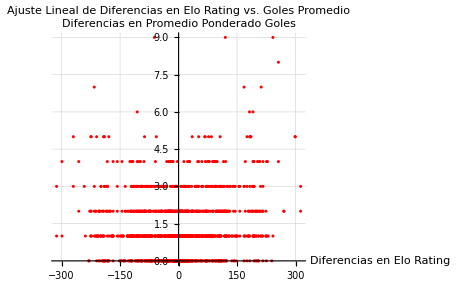

```mathematica
Show[
  ListPlot[Transpose[{trainDataSet[All,"DifferenceELO"]//Normal,trainDataSet[All,"DifferenceGoals"]//Normal}], PlotStyle -> Red, 
   AxesLabel -> {"Diferencias en Elo Rating", "Diferencias en Promedio Ponderado Goles"}, 
   PlotLabel -> "Ajuste Lineal de Diferencias en Elo Rating vs. Goles Promedio", 
   GridLines -> Automatic]
  (*Plot[modelFit, {x, Min[eloDifferences], Max[eloDifferences]}, PlotStyle -> Blue]*)
]
```

## Model